```mathematica
(* test single values *)
```

```mathematica
thebr0gauss=10^(15);
myfakemu=10^4;
consts={M->3*msun,Mdot->0.1*msun,AM->0.2,mueq->myfakemu,C0->3,C1->2,C2->0.4,nucoll->3/4,rmono->3*10^(10),Br0gauss->thebr0gauss, Br0->Br0gauss/Sqrt[4*Pi],rfp->rl ,rfinal->10^(15),thfinal->0.02,Bphi0->Br0*1.00};
toplot:=mygammafinal[r,Evaluate[thofr[r,thfp]//.consts]]//.consts;
toplotmu:=mutest[r,Evaluate[thofr[r,thfp]//.consts]]//.consts;
```

```mathematica
mygamma=toplot//.{r->10^16}
mymu=toplotmu//.{r->10^16}
mytheta=Evaluate[thofr[r,thfp]//.consts]//.{r->10^16}
mygamma*mytheta
```

740.963

4331.28

0.0218269

16.1729

```mathematica
mygamma/mymu
mygamma/myfakemu
```

0.00977218

0.00423149

```mathematica
(* mu = gamma*(1+sigma) *)
mysigma=mymu/mygamma-1
```

101.331

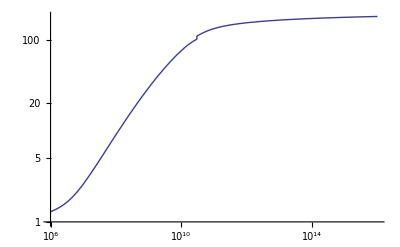

```mathematica
LogLogPlot[toplot,{r,10^6,10^(16)}]
```

```mathematica
(* Get expression *)
```

```mathematica
nb1=NotebookOpen["D:\\Super Documents\\math\\private\\gamma_jet_simpleseriesetc.nb"];
SelectionMove[nb1,All,Notebook]
SelectionEvaluate[nb1]

nb2=NotebookOpen["D:\\Super Documents\\math\\private\\gamma_jet_reconnection_simpleseriesetc.nb"];
SelectionMove[nb2,All,Notebook]
SelectionEvaluate[nb2]
```

```mathematica
(* test *)
Aphi[r,th]
thofr[r,thfp]
thfpofrth[r,th]
omegaf[r,th]
Br[r,th]
Bh[r,th]
Bp[r,th]
Bphistart[r,th]
vpfp[r,th]
rho0fp[r,th]
omegaffp[r,th]
Rfp[r,th]
Bphifp[r,th]
Bpfp[r,th]
vphifp[r,th]
vsqfp[r,th]
gammafp[r,th]
upfp[r,th]
uphifp[r,th]
Phi1fp[r,th]
Phi2fp[r,th]
lambdafp[r,th]
mufp[r,th]
gamma1[r,th]
mygammafinal[r,th]
uphi[r,th]
up[r,th]
rho0[r,th]
Bphi[r,th]
bsq[r,th]
```

Aphi[r,th]

thofr[r,thfp]

thfpofrth[r,th]

omegaf[r,th]

Br[r,th]

Bh[r,th]

Bp[r,th]

Bphistart[r,th]

vpfp[r,th]

rho0fp[r,th]

omegaffp[r,th]

Rfp[r,th]

Bphifp[r,th]

Bpfp[r,th]

vphifp[r,th]

vsqfp[r,th]

gammafp[r,th]

upfp[r,th]

uphifp[r,th]

Phi1fp[r,th]

Phi2fp[r,th]

lambdafp[r,th]

mufp[r,th]

gamma1[r,th]

mygammafinal[r,th]

uphi[r,th]

up[r,th]

rho0[r,th]

Bphi[r,th]

(Bp[r,0]^2+Bphi[r,0]^2+(Bp[r,0] up[r,0]+Bphi[r,0] uphi[r,0])^2/c^2)/mygammafinal[r,0]^2+th (-(2 (Bp[r,0]^2+Bphi[r,0]^2+(Bp[r,0] up[r,0]+Bphi[r,0] uphi[r,0])^2/c^2) mygammafinal^(0,1)[r,0])/mygammafinal[r,0]^3+(2 Bp[r,0] Bp^(0,1)[r,0]+2 Bphi[r,0] Bphi^(0,1)[r,0]+(2 (Bp[r,0] up[r,0]+Bphi[r,0] uphi[r,0]) (up[r,0] Bp^(0,1)[r,0]+uphi[r,0] Bphi^(0,1)[r,0]+Bp[r,0] up^(0,1)[r,0]+Bphi[r,0] uphi^(0,1)[r,0]))/c^2)/mygammafinal[r,0]^2)+th^2 (-(2 mygammafinal^(0,1)[r,0] (2 Bp[r,0] Bp^(0,1)[r,0]+2 Bphi[r,0] Bphi^(0,1)[r,0]+(2 (Bp[r,0] up[r,0]+Bphi[r,0] uphi[r,0]) (up[r,0] Bp^(0,1)[r,0]+uphi[r,0] Bphi^(0,1)[r,0]+Bp[r,0] up^(0,1)[r,0]+Bphi[r,0] uphi^(0,1)[r,0]))/c^2))/mygammafinal[r,0]^3+(Bp[r,0]^2+Bphi[r,0]^2+(Bp[r,0] up[r,0]+Bphi[r,0] uphi[r,0])^2/c^2) ((3 (mygammafinal^(0,1)[r,0])^2)/mygammafinal[r,0]^4-(mygammafinal^(0,2)[r,0])/mygammafinal[r,0]^3)+1/mygammafinal[r,0]^2((Bp^(0,1)[r,0])^2+(Bphi^(0,1)[r,0])^2+Bp[r,0] Bp^(0,2)[r,0]+Bphi[r,0] Bphi^(0,2)[r,0]+1/c^2((up[r,0] Bp^(0,1)[r,0]+uphi[r,0] Bphi^(0,1)[r,0]+Bp[r,0] up^(0,1)[r,0]+Bphi[r,0] uphi^(0,1)[r,0])^2+2 (Bp[r,0] up[r,0]+Bphi[r,0] uphi[r,0]) (Bp^(0,1)[r,0] up^(0,1)[r,0]+Bphi^(0,1)[r,0] uphi^(0,1)[r,0]+1/2 up[r,0] Bp^(0,2)[r,0]+1/2 uphi[r,0] Bphi^(0,2)[r,0]+1/2 Bp[r,0] up^(0,2)[r,0]+1/2 Bphi[r,0] uphi^(0,2)[r,0]))))

```mathematica
sols=Solve[eqgamma2m,gamma2m]
```

{{gamma2m→-((2/3)^(1/3) C1^3 Csc[th]^2 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))])/(9 C1^3 mufpfunc Csc[th]^2 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))]+√3 √(27 C1^6 mufpfunc^2 Csc[th]^4 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))]^2+4 C1^9 Csc[th]^6 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))]^3))^(1/3)+1/(2^(1/3) 3^(2/3))(9 C1^3 mufpfunc Csc[th]^2 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))]+√3 √(27 C1^6 mufpfunc^2 Csc[th]^4 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))]^2+4 C1^9 Csc[th]^6 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))]^3))^(1/3)},{gamma2m→((1+ⅈ √3) C1^3 Csc[th]^2 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))])/(2^(2/3) 3^(1/3) (9 C1^3 mufpfunc Csc[th]^2 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))]+√3 √(27 C1^6 mufpfunc^2 Csc[th]^4 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))]^2+4 C1^9 Csc[th]^6 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))]^3))^(1/3))-1/(2 2^(1/3) 3^(2/3))(1-ⅈ √3) (9 C1^3 mufpfunc Csc[th]^2 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))]+√3 √(27 C1^6 mufpfunc^2 Csc[th]^4 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))]^2+4 C1^9 Csc[th]^6 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))]^3))^(1/3)},{gamma2m→((1-ⅈ √3) C1^3 Csc[th]^2 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))])/(2^(2/3) 3^(1/3) (9 C1^3 mufpfunc Csc[th]^2 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))]+√3 √(27 C1^6 mufpfunc^2 Csc[th]^4 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))]^2+4 C1^9 Csc[th]^6 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))]^3))^(1/3))-1/(2 2^(1/3) 3^(2/3))(1+ⅈ √3) (9 C1^3 mufpfunc Csc[th]^2 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))]+√3 √(27 C1^6 mufpfunc^2 Csc[th]^4 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))]^2+4 C1^9 Csc[th]^6 Log[1+(C2 omegaffunc r Sin[th])/(c (mufpfunc Csc[th]^2)^(1/3))]^3))^(1/3)}}

```mathematica
tempmygamma2m
```

-((2/3)^(1/3) C1^3 Csc[th]^2 Log[1+(C2 r Sin[th])/(4 c tl ((1/(√(3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2)))-(Bphi0 √(Br0^2 rfp^4) th)/(16 Br0^2 c^2 rfp^2 (3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2))^(3/2) tl^2)) Csc[th]^2)^(1/3))])/(9 C1^3 (1/(√(3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2)))-(Bphi0 √(Br0^2 rfp^4) th)/(16 Br0^2 c^2 rfp^2 (3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2))^(3/2) tl^2)) Csc[th]^2 Log[1+(C2 r Sin[th])/(4 c tl ((1/(√(3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2)))-(Bphi0 √(Br0^2 rfp^4) th)/(16 Br0^2 c^2 rfp^2 (3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2))^(3/2) tl^2)) Csc[th]^2)^(1/3))]+√3 √(27 C1^6 (1/(√(3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2)))-(Bphi0 √(Br0^2 rfp^4) th)/(16 Br0^2 c^2 rfp^2 (3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2))^(3/2) tl^2))^2 Csc[th]^4 Log[1+(C2 r Sin[th])/(4 c tl ((1/(√(3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2)))-(Bphi0 √(Br0^2 rfp^4) th)/(16 Br0^2 c^2 rfp^2 (3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2))^(3/2) tl^2)) Csc[th]^2)^(1/3))]^2+4 C1^9 Csc[th]^6 Log[1+(C2 r Sin[th])/(4 c tl ((1/(√(3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2)))-(Bphi0 √(Br0^2 rfp^4) th)/(16 Br0^2 c^2 rfp^2 (3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2))^(3/2) tl^2)) Csc[th]^2)^(1/3))]^3))^(1/3)+1/(2^(1/3) 3^(2/3))(9 C1^3 (1/(√(3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2)))-(Bphi0 √(Br0^2 rfp^4) th)/(16 Br0^2 c^2 rfp^2 (3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2))^(3/2) tl^2)) Csc[th]^2 Log[1+(C2 r Sin[th])/(4 c tl ((1/(√(3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2)))-(Bphi0 √(Br0^2 rfp^4) th)/(16 Br0^2 c^2 rfp^2 (3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2))^(3/2) tl^2)) Csc[th]^2)^(1/3))]+√3 √(27 C1^6 (1/(√(3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2)))-(Bphi0 √(Br0^2 rfp^4) th)/(16 Br0^2 c^2 rfp^2 (3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2))^(3/2) tl^2))^2 Csc[th]^4 Log[1+(C2 r Sin[th])/(4 c tl ((1/(√(3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2)))-(Bphi0 √(Br0^2 rfp^4) th)/(16 Br0^2 c^2 rfp^2 (3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2))^(3/2) tl^2)) Csc[th]^2)^(1/3))]^2+4 C1^9 Csc[th]^6 Log[1+(C2 r Sin[th])/(4 c tl ((1/(√(3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2)))-(Bphi0 √(Br0^2 rfp^4) th)/(16 Br0^2 c^2 rfp^2 (3/4-Bphi0^2/(16 Br0^2 c^2 rfp^2 tl^2))^(3/2) tl^2)) Csc[th]^2)^(1/3))]^3))^(1/3)

```mathematica
Clear[Ljet,Lp,thfp];
consts={};
Ljet=r;
setupvalues;
setupgettemperature;
gettemperature;
(*gettemperaturegeneral*)
gettaualongjet;
reportpressure;
getDelta;
getlarmor;
getDeltasp;
getconditoine;
getconditoinp;
getTobs;
gettimeann;
gettaus;
getTdiffs;
getdtobs;
solsT
```

thetajet in degrees

Bphivalue

taurad

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

P components

Tann

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

FullSimplify::fas: Warning: One or more assumptions evaluated to False.

General::stop: Further output of FullSimplify will be suppressed during this calculation.

FullSimplify::fas: Warning: One or more assumptions evaluated to False.

General::stop: Further output of FullSimplify will be suppressed during this calculation.

Observed value in MeV

myn

{{}}

```mathematica
thetajet
```

(√(Br0^2 r^4) rfp^2 th)/(2 r^2)

```mathematica
getconstants;
gammavalue//.{ Br0->Br0gauss/Sqrt[4*Pi],Br0gauss->10^(15),r->10^(15),rfp->10^6,th->0.01,G->6.672*10^(-8) ,c->2.99792458*10^(10),C0->3,C1->2,C2->0.4,Bphi0->Br0*1 ,mueq->10^4}
```

arad

1.32593+1.87019×10^24 (-3.85481×10^39-1.32593 √(-(-0.318521-(-7.59639×10^99+7.59639×10^99 sgamma^2-8.45212×10^78 uph^2) (-8.98755×10^20+8.98755×10^20 sgamma^2-uph^2))/(8.98755×10^20-8.98755×10^20 sgamma^2+uph^2)^2))

```mathematica
conditionpc//.{bsq->1,Rjet->1,rhobvalue->1}
```

Indeterminate

```mathematica
FullSimplify[conditionpc,{bsq>0,Rjet>0,rhobvalue>0}
```

392102./(√((bsq ⅇ^(0./Rjet) Rjet)/((7.35089×10^9+5.06683×10^12 bsq^(3/4) ⅇ^(-(1.58029×10^6 ⅇ^(-5.11361×10^13/Rjet))/bsq^(1/4)-2.2208×10^-18 √(7.35089×10^9+5.06683×10^12 bsq^(3/4) ⅇ^(-(1.58029×10^6 ⅇ^(-5.11361×10^13/Rjet))/bsq^(1/4)-(5.11361×10^13)/Rjet))-(5.11361×10^13)/Rjet)) √(bsqvalue/(bsqvalue+2. bsq ⅇ^(0./Rjet)+8.98755×10^20 rhobvalue)))))